```mathematica
dados1 = Import["/home/joao/Documents/1MEFT/2.ba ano/2.ba Ano 1.ba Semestre/FC/2017_2018/Laboratorio/Series//s3c4/quantumKutta.dat", "Table"];
```

```mathematica
dados1
```

{{0,1},{0.01,0.990443},{0.02,0.961955},{0.03,0.915081},{0.04,0.850715},{0.05,0.77009},{0.06,0.674746},{0.07,0.566504},{0.08,0.447435},{0.09,0.319815},{0.1,0.186081},{0.11,0.0487911},{0.12,-0.0894314},{0.13,-0.225945},{0.14,-0.35814},{0.15,-0.48349},{0.16,-0.5996},{0.17,-0.704251},{0.18,-0.795442},{0.19,-0.871433},{0.2,-0.93077},{0.21,-0.97232},{0.22,-0.995289},{0.23,-0.999239},{0.24,-0.984096},{0.25,-0.950147},{0.26,-0.898044},{0.27,-0.828781},{0.28,-0.743683},{0.29,-0.644377},{0.3,-0.532759},{0.31,-0.410962},{0.32,-0.281314},{0.33,-0.146292},{0.34,-0.00847596},{0.35,0.129502},{0.36,0.265007},{0.37,0.39545},{0.38,0.518339},{0.39,0.631329},{0.4,0.73226},{0.41,0.819207},{0.42,0.890509},{0.43,0.944806},{0.44,0.98106},{0.45,0.998582},{0.46,0.997036},{0.47,0.976454},{0.48,0.937229},{0.49,0.880112},{0.5,0.806193},{0.51,0.716884},{0.52,0.613891},{0.53,0.49918},{0.54,0.374942},{0.55,0.243548},{0.56,0.107506},{0.57,-0.0305869},{0.58,-0.168097},{0.59,-0.302399},{0.6,-0.430932},{0.61,-0.551243},{0.62,-0.661038},{0.63,-0.758223},{0.64,-0.840945},{0.65,-0.907627},{0.66,-0.956999},{0.67,-0.98812},{0.68,-1.0004},{0.69,-0.993599},{0.7,-0.967856},{0.71,-0.92366},{0.72,-0.861856},{0.73,-0.783621},{0.74,-0.690451},{0.75,-0.58412},{0.76,-0.466656},{0.77,-0.3403},{0.78,-0.207459},{0.79,-0.0706651},{0.8,0.0674752},{0.81,0.20433},{0.82,0.337292},{0.83,0.46383},{0.84,0.581534},{0.85,0.688163},{0.86,0.781688},{0.87,0.860329},{0.88,0.922589},{0.89,0.967286},{0.9,0.99357},{0.91,1.00094},{0.92,0.989265},{0.93,0.958762},{0.94,0.910015},{0.95,0.843953},{0.96,0.761835},{0.97,0.665225},{0.98,0.555962},{0.99,0.436125},{1,0.307994},{1.01,0.174006},{1.02,0.0367102},{1.03,-0.101284},{1.04,-0.237352},{1.05,-0.36891},{1.06,-0.493456},{1.07,-0.608625},{1.08,-0.71223},{1.09,-0.802304},{1.1,-0.877136},{1.11,-0.935309},{1.12,-0.975718},{1.13,-0.997598},{1.14,-1.00054},{1.15,-0.984479},{1.16,-0.949733},{1.17,-0.896961},{1.18,-0.827165},{1.19,-0.741673},{1.2,-0.642109},{1.21,-0.530363},{1.22,-0.408557},{1.23,-0.279002},{1.24,-0.144155},{1.25,-0.0065754},{1.26,0.131129},{1.27,0.266348},{1.28,0.396519},{1.29,0.519174},{1.3,0.631992},{1.31,0.732836},{1.32,0.819797},{1.33,0.89123},{1.34,0.945785},{1.35,0.982429},{1.36,1.00047},{1.37,0.999578},{1.38,0.979762},{1.39,0.941404},{1.4,0.885233},{1.41,0.812312},{1.42,0.724026},{1.43,0.622045},{1.44,0.5083},{1.45,0.384944},{1.46,0.25431},{1.47,0.11887},{1.48,-0.018818},{1.49,-0.15615},{1.5,-0.290532},{1.51,-0.419425},{1.52,-0.540396},{1.53,-0.651162},{1.54,-0.749633},{1.55,-0.833952},{1.56,-0.902529},{1.57,-0.954073},{1.58,-0.987614},{1.59,-1.00252},{1.6,-0.99852},{1.61,-0.975685},{1.62,-0.934452},{1.63,-0.875601},{1.64,-0.800244},{1.65,-0.709804},{1.66,-0.60599},{1.67,-0.490757},{1.68,-0.36628},{1.69,-0.234905},{1.7,-0.099106},{1.71,0.0385589},{1.72,0.175498},{1.73,0.309134},{1.74,0.436954},{1.75,0.556552},{1.76,0.665682},{1.77,0.762293},{1.78,0.84457},{1.79,0.910969},{1.8,0.960246},{1.81,0.991477},{1.82,1.00408},{1.83,0.99782},{1.84,0.97282},{1.85,0.929552},{1.86,0.868832},{1.87,0.791804},{1.88,0.699915},{1.89,0.594894},{1.9,0.478713},{1.91,0.353553},{1.92,0.221763},{1.93,0.0858158},{1.94,-0.0517404},{1.95,-0.188327},{1.96,-0.321385},{1.97,-0.448423},{1.98,-0.567062},{1.99,-0.675083},{2,-0.770466},{2.01,-0.851428},{2.02,-0.916458},{2.03,-0.964341},{2.04,-0.994187},{2.05,-1.00544},{2.06,-0.997895},{2.07,-0.971696},{2.08,-0.927338},{2.09,-0.865653},{2.1,-0.787796},{2.11,-0.695227},{2.12,-0.589677},{2.13,-0.473118},{2.14,-0.347729},{2.15,-0.215852},{2.16,-0.0799475},{2.17,0.0574478},{2.18,0.193772},{2.19,0.326484},{2.2,0.453111},{2.21,0.571295},{2.22,0.678837},{2.23,0.773735},{2.24,0.854227},{2.25,0.918816},{2.26,0.966305},{2.27,0.995814},{2.28,1.0068},{2.29,0.999059},{2.3,0.972744},{2.31,0.928346},{2.32,0.866696},{2.33,0.788943},{2.34,0.696536},{2.35,0.591193},{2.36,0.474875},{2.37,0.349743},{2.38,0.21812},{2.39,0.0824511},{2.4,-0.0547472},{2.41,-0.19093},{2.42,-0.323575},{2.43,-0.450222},{2.44,-0.568528},{2.45,-0.676304},{2.46,-0.771556},{2.47,-0.852524},{2.48,-0.917714},{2.49,-0.965923},{2.5,-0.996264},{2.51,-1.00818},{2.52,-1.00146},{2.53,-0.976227},{2.54,-0.932956},{2.55,-0.87245},{2.56,-0.795831},{2.57,-0.704519},{2.58,-0.600203},{2.59,-0.484812},{2.6,-0.360477},{2.61,-0.229493},{2.62,-0.0942785},{2.63,0.0426741},{2.64,0.17884},{2.65,0.311712},{2.66,0.438844},{2.67,0.557896},{2.68,0.666679},{2.69,0.763196},{2.7,0.845673},{2.71,0.912599},{2.72,0.962747},{2.73,0.995202},{2.74,1.00937},{2.75,1.005},{2.76,0.982173},{2.77,0.941317},{2.78,0.883187},{2.79,0.808853},{2.8,0.719685},{2.81,0.617321},{2.82,0.503642},{2.83,0.380734},{2.84,0.250851},{2.85,0.116375},{2.86,-0.0202317},{2.87,-0.156468},{2.88,-0.289842},{2.89,-0.417916},{2.9,-0.538348},{2.91,-0.64894},{2.92,-0.747674},{2.93,-0.832751},{2.94,-0.902621},{2.95,-0.956014},{2.96,-0.991961},{2.97,-1.00981},{2.98,-1.00924},{2.99,-0.990278},{3,-0.953263},{3.01,-0.89888},{3.02,-0.828126},{3.03,-0.742293},{3.04,-0.642949},{3.05,-0.531906},{3.06,-0.411188},{3.07,-0.282994},{3.08,-0.149655},{3.09,-0.0135961},{3.1,0.122709},{3.11,0.256787},{3.12,0.386203},{3.13,0.508611},{3.14,0.621793},{3.15,0.7237},{3.16,0.812487},{3.17,0.886551},{3.18,0.944555},{3.19,0.985455},{3.2,1.00852},{3.21,1.01333},{3.22,0.999805},{3.23,0.968204},{3.24,0.919101},{3.25,0.85339},{3.26,0.772263},{3.27,0.67719},{3.28,0.569894},{3.29,0.452314},{3.3,0.326575},{3.31,0.194947},{3.32,0.0598051},{3.33,-0.0764144},{3.34,-0.211258},{3.35,-0.342297},{3.36,-0.467177},{3.37,-0.583651},{3.38,-0.689628},{3.39,-0.783207},{3.4,-0.86271},{3.41,-0.926716},{3.42,-0.974079},{3.43,-1.00396},{3.44,-1.01582},{3.45,-1.00946},{3.46,-0.985001},{3.47,-0.942887},{3.48,-0.88388},{3.49,-0.809042},{3.5,-0.719719},{3.51,-0.617517},{3.52,-0.504267},{3.53,-0.382},{3.54,-0.252905},{3.55,-0.119291},{3.56,0.0164545},{3.57,0.151906},{3.58,0.284647},{3.59,0.41231},{3.6,0.53262},{3.61,0.643437},{3.62,0.742788},{3.63,0.82891},{3.64,0.900275},{3.65,0.955617},{3.66,0.99396},{3.67,1.01463},{3.68,1.01726},{3.69,1.00182},{3.7,0.96859},{3.71,0.918162},{3.72,0.851441},{3.73,0.769618},{3.74,0.674148},{3.75,0.56673},{3.76,0.449273},{3.77,0.323859},{3.78,0.192713},{3.79,0.0581569},{3.8,-0.0774279},{3.81,-0.211644},{3.82,-0.342121},{3.83,-0.466554},{3.84,-0.582751},{3.85,-0.688664},{3.86,-0.782429},{3.87,-0.862398},{3.88,-0.927168},{3.89,-0.975604},{3.9,-1.00686},{3.91,-1.0204},{3.92,-1.01598},{3.93,-0.993694},{3.94,-0.953942},{3.95,-0.89743},{3.96,-0.825157},{3.97,-0.738398},{3.98,-0.638683},{3.99,-0.527767},{4,-0.407598},{4.01,-0.280286},{4.02,-0.148066},{4.03,-0.0132532},{4.04,0.121792},{4.05,0.254707},{4.06,0.383169},{4.07,0.504935},{4.08,0.617882},{4.09,0.720043},{4.1,0.809638},{4.11,0.885112},{4.12,0.945156},{4.13,0.988729},{4.14,1.01508},{4.15,1.02376},{4.16,1.01463},{4.17,0.987847},{4.18,0.943893},{4.19,0.883538},{4.2,0.807838},{4.21,0.718114},{4.22,0.61593},{4.23,0.503064},{4.24,0.381478},{4.25,0.253282},{4.26,0.1207},{4.27,-0.0139712},{4.28,-0.148401},{4.29,-0.280265},{4.3,-0.407285},{4.31,-0.52727},{4.32,-0.638151},{4.33,-0.738019},{4.34,-0.825158},{4.35,-0.89807},{4.36,-0.955508},{4.37,-0.996489},{4.38,-1.02032},{4.39,-1.02659},{4.4,-1.01521},{4.41,-0.986375},{4.42,-0.940598},{4.43,-0.878671},{4.44,-0.801664},{4.45,-0.710907},{4.46,-0.607961},{4.47,-0.494598},{4.48,-0.372765},{4.49,-0.24455},{4.5,-0.112151},{4.51,0.0221654},{4.52,0.156103},{4.53,0.287375},{4.54,0.413741},{4.55,0.533047},{4.56,0.643262},{4.57,0.742514},{4.58,0.829115},{4.59,0.9016},{4.6,0.958741},{4.61,0.999575},{4.62,1.02342},{4.63,1.02987},{4.64,1.01884},{4.65,0.99051},{4.66,0.945382},{4.67,0.884227},{4.68,0.808089},{4.69,0.718266},{4.7,0.616285},{4.71,0.50388},{4.72,0.382956},{4.73,0.25556},{4.74,0.123848},{4.75,-0.00995409},{4.76,-0.143589},{4.77,-0.274803},{4.78,-0.401386},{4.79,-0.521211},{4.8,-0.632263},{4.81,-0.732679},{4.82,-0.820778},{4.83,-0.895086},{4.84,-0.954364},{4.85,-0.997624},{4.86,-1.02415},{4.87,-1.03351},{4.88,-1.02555},{4.89,-1.00042},{4.9,-0.958551},{4.91,-0.900648},{4.92,-0.827691},{4.93,-0.740907},{4.94,-0.641752},{4.95,-0.53189},{4.96,-0.413158},{4.97,-0.28754},{4.98,-0.157132},{4.99,-0.0241087},{5,0.109316},{5.01,0.240923},{5.02,0.368528},{5.03,0.490013},{5.04,0.603365},{5.05,0.70671},{5.06,0.798341},{5.07,0.876747},{5.08,0.940637},{5.09,0.988964},{5.1,1.02094},{5.11,1.03604},{5.12,1.03403},{5.13,1.01495},{5.14,0.979137},{5.15,0.927179},{5.16,0.859946},{5.17,0.778554},{5.18,0.684352},{5.19,0.578896},{5.2,0.463927},{5.21,0.341339},{5.22,0.213148},{5.23,0.081461},{5.24,-0.0515615},{5.25,-0.18374},{5.26,-0.31291},{5.27,-0.436961},{5.28,-0.553868},{5.29,-0.661726},{5.3,-0.758778},{5.31,-0.843449},{5.32,-0.914365},{5.33,-0.970379},{5.34,-1.01059},{5.35,-1.03435},{5.36,-1.04129},{5.37,-1.0313},{5.38,-1.00456},{5.39,-0.961513},{5.4,-0.902868},{5.41,-0.829584},{5.42,-0.742861},{5.43,-0.644111},{5.44,-0.534939},{5.45,-0.417117},{5.46,-0.292556},{5.47,-0.163271},{5.48,-0.0313505},{5.49,0.101075},{5.5,0.231873},{5.51,0.358936},{5.52,0.480224},{5.53,0.59379},{5.54,0.697813},{5.55,0.79063},{5.56,0.87076},{5.57,0.936925},{5.58,0.988075},{5.59,1.0234},{5.6,1.04235},{5.61,1.04463},{5.62,1.03021},{5.63,0.999342},{5.64,0.952524},{5.65,0.890516},{5.66,0.814316},{5.67,0.725148},{5.68,0.624439},{5.69,0.5138},{5.7,0.394996},{5.71,0.269919},{5.72,0.140558},{5.73,0.00896887},{5.74,-0.122763},{5.75,-0.252551},{5.76,-0.378344},{5.77,-0.498154},{5.78,-0.610094},{5.79,-0.712402},{5.8,-0.80347},{5.81,-0.881871},{5.82,-0.94638},{5.83,-0.995991},{5.84,-1.02993},{5.85,-1.04769},{5.86,-1.04899},{5.87,-1.03382},{5.88,-1.00244},{5.89,-0.955345},{5.9,-0.893292},{5.91,-0.81726},{5.92,-0.728448},{5.93,-0.628254},{5.94,-0.51825},{5.95,-0.400161},{5.96,-0.275833},{5.97,-0.147208},{5.98,-0.0162909},{5.99,0.11488},{6,0.244265},{6.01,0.369857},{6.02,0.48971},{6.03,0.601969},{6.04,0.704902},{6.05,0.796921},{6.06,0.876612},{6.07,0.942753},{6.08,0.994331},{6.09,1.03056},{6.1,1.0509},{6.11,1.05505},{6.12,1.04295},{6.13,1.0148},{6.14,0.971058},{6.15,0.912395},{6.16,0.839729},{6.17,0.754183},{6.18,0.657081},{6.19,0.549918},{6.2,0.43434},{6.21,0.312123},{6.22,0.185138},{6.23,0.0553271},{6.24,-0.0753278},{6.25,-0.204835},{6.26,-0.331224},{6.27,-0.452575},{6.28,-0.567046},{6.29,-0.672906},{6.3,-0.768555},{6.31,-0.852551},{6.32,-0.923631},{6.33,-0.980729},{6.34,-1.023},{6.35,-1.0498},{6.36,-1.06076},{6.37,-1.05571},{6.38,-1.03475},{6.39,-0.998199},{6.4,-0.94663},{6.41,-0.880828},{6.42,-0.801793},{6.43,-0.710723},{6.44,-0.608993},{6.45,-0.498138},{6.46,-0.379824},{6.47,-0.255829},{6.48,-0.128009},{6.49,0.00172189},{6.5,0.131428},{6.51,0.259175},{6.52,0.383062},{6.53,0.501249},{6.54,0.611983},{6.55,0.713626},{6.56,0.804678},{6.57,0.883797},{6.58,0.949822},{6.59,1.00179},{6.6,1.03894},{6.61,1.06073},{6.62,1.06687},{6.63,1.05727},{6.64,1.03209},{6.65,0.99171},{6.66,0.936744},{6.67,0.86801},{6.68,0.786529},{6.69,0.69351},{6.7,0.590325},{6.71,0.478495},{6.72,0.359664},{6.73,0.235575},{6.74,0.108046},{6.75,-0.0210597},{6.76,-0.149859},{6.77,-0.276476},{6.78,-0.39907},{6.79,-0.515864},{6.8,-0.625166},{6.81,-0.725397},{6.82,-0.815113},{6.83,-0.893025},{6.84,-0.958016},{6.85,-1.00916},{6.86,-1.04573},{6.87,-1.06721},{6.88,-1.07331},{6.89,-1.06395},{6.9,-1.03928},{6.91,-0.999683},{6.92,-0.945726},{6.93,-0.878202},{6.94,-0.798092},{6.95,-0.706555},{6.96,-0.604911},{6.97,-0.494622},{6.98,-0.377272},{6.99,-0.254541},{7,-0.128183}}

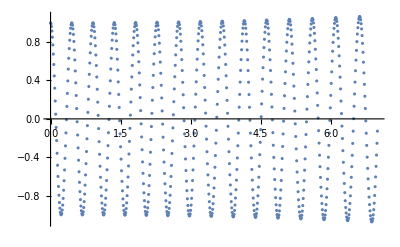

```mathematica
ListPlot[dados1]
```